```mathematica
Clear["Global`*"]
```

## NIG factor model stuff

```mathematica
Clear[α,β,μ,δ,μ1,μ2,δ1,δ2]
```

See https://en.wikipedia.org/wiki/Bessel_function: The modified Bessel function of the second kind has also been called [..] Modified Bessel function of the t

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]);
```

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u]
```

Expectation

```mathematica
Simplify[D[M[u,α,β,μ,δ], u]/.u->0]
```

(β δ)/(√(α^2-β^2))+μ

```mathematica
ENIG[α_,β_,μ_,δ_]:=μ+(δ β)/(√(α^2-β^2));
```

Variance

```mathematica
Simplify[D[M[u,α,β,μ,δ], {u,2}]-ENIG[α,β,μ,δ]^2/.u->0]
```

(α^2 δ)/((α^2-β^2)^(3/2))

```mathematica
VNIG[α_,β_,μ_,δ_]:=(α^2 δ)/((α^2-β^2)^(3/2));
```

Skewness
(see https://en.wikipedia.org/wiki/Skewness)

```mathematica
Simplify[(D[M[u,α,β,μ,δ], {u,3}]-3 ENIG[α,β,μ,δ] VNIG[α,β,μ,δ]-ENIG[α,β,μ,δ]^3)/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
SNIG[α_,β_,μ_,δ_]:=(3 β)/(α √δ (α^2-β^2)^(1/4))
```

Centering inside the moment generating function:

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

Kurtosis

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,4}]/VNIG[α,β,μ,δ]^2/.u->0,Assumptions->α>0]
```

(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3

```mathematica
KNIG[α_,β_,μ_,δ_]:=(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3
```

Simulate  NIG’s 
-Graphics-

```mathematica
d[x_,α_,β_,δ_]:=(Exp[δ √(α^2-β^2)] x^(-3/2) Exp[-(δ^2/x+(α^2-β^2) x)/2])/(√(2 π))
```

```mathematica
μ=0;
μ1=-1;
μ2=0.5;
δ=0.5;
δ1=2;
δ2=1;
β=-3;
α=8;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
n=10000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
```

```mathematica
X1 = Z + Z1;
X2 = Z + Z2;
```

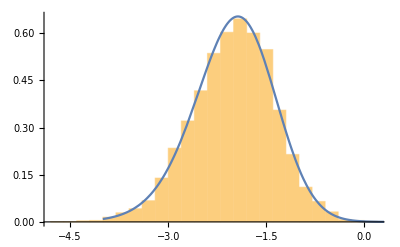
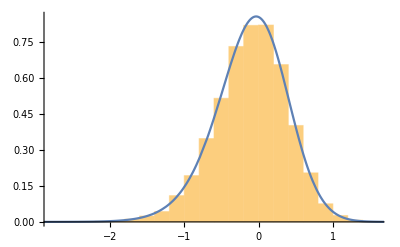

```mathematica
{Show[
Histogram[X1,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ1,δ+δ1], {x,-4,5}]
],
Show[
Histogram[X2,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ2,δ+δ2], {x,-4,5},PlotRange->Full]
]}
```

```mathematica
EX1=ENIG[α, β, μ+μ1,δ+δ1];
EX2=ENIG[α, β,μ+μ2,δ+δ2];
```

```mathematica
VX1=VNIG[α,β,μ+μ1,δ+δ1];
VX2=VNIG[α,β, μ+μ2,δ+δ2];
VZ = VNIG[α,β,μ,δ];
```

```mathematica
N[{{Mean[X1], EX1}, {Variance[X1], VX1}, {Mean[X2],EX2}, {Variance[X2], VX2}}//TableForm]
```

-2.00653 | -2.0113
0.392081 | 0.392262
-0.0995259 | -0.10678
0.236791 | 0.235357

Covariance

```mathematica
N[{VZ, Covariance[X1,X2]}]
```

{0.0784523,0.0802196}

-Graphics-

Correlation

```mathematica
N[{√(δ^2/((δ+δ1) (δ+δ2))),Correlation[X1,X2]}]
```

{0.258199,0.263275}

```mathematica
N[Table[{Moment[X1,r],D[M[u,α,β,μ+μ1, δ+δ1], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-2.00653 | -2.0113
4.41819 | 4.43759
-10.5014 | -10.5674
26.6777 | 26.9025
-71.917 | -72.7361
204.578 | 207.833
-611.256 | -625.235
1910.74 | 1974.3
-6226.57 | -6527.34
21083.3 | 22547.5

```mathematica
N[Table[{Moment[X2,r],D[M[u,α,β,μ+μ2, δ+δ2], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-0.0995259 | -0.10678
0.246672 | 0.246759
-0.114712 | -0.115125
0.229271 | 0.222201
-0.234962 | -0.213612
0.458671 | 0.407466
-0.731378 | -0.60406
1.50983 | 1.24808
-3.00078 | -2.44571
6.59539 | 5.69069

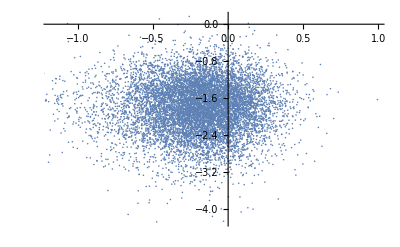
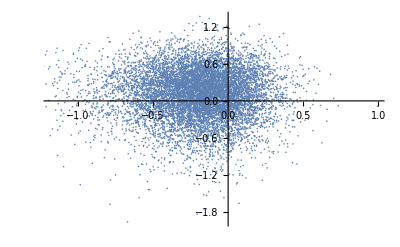

```mathematica
{ListPlot[{Z,Z1}ᵀ], ListPlot[{Z,Z2}ᵀ]}
```

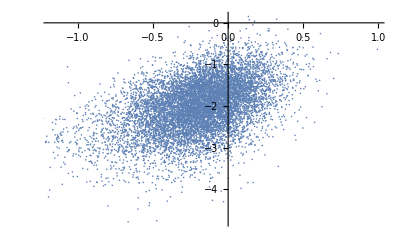
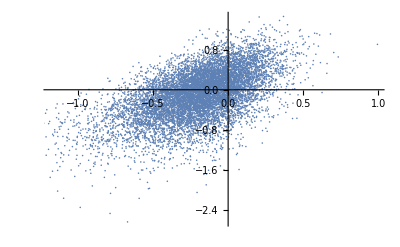

```mathematica
{ListPlot[{Z,X1}ᵀ],ListPlot[{Z,X2}ᵀ]}
```

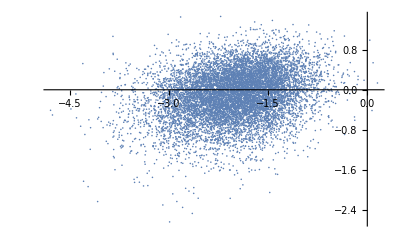

```mathematica
ListPlot[{X1, X2}ᵀ]
```

#### ML estimates of parameters

This is either very slow or very imprecise.

```mathematica
Timing[LL[α_,β_,μ_,δ_]:=Total[Log[g[X1⟦1;;1000⟧,α,β,μ,δ]]];NMaximize[{LL[α0,-3,-1,2.5],α0>5}, α0]]
```

{11.5518,{-977.051,{α0→7.83046}}}

```mathematica
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

{-977.993,{8,-3,-1,2.5}}

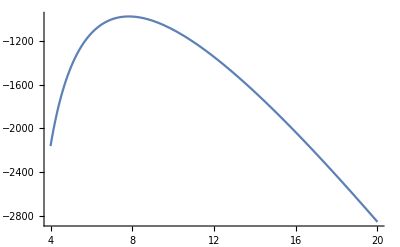

```mathematica
Plot[LL[α0, -3, -1, 2.5], {α0,4,20}]
```

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X1[[1;;1000]],α,β,μ,δ]]];Timing[NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]]
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

{25.9023,{-974.588,{α0→9.56415,β0→-1.67332,μ0→-1.36374,δ0→3.75909}}}

{-977.993,{8,-3,-1,2.5}}

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X2[[1;;1000]],α,β,μ,δ]]];NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]
{LL[α,β,μ+μ2,δ+δ2],{α,β,μ+μ2,δ+δ2}}
```

{-642.151,{α0→7.50639,β0→-3.61695,μ0→0.517785,δ0→1.1147}}

{-646.294,{8,-3,0.5,1.5}}

#### Method of moments

This performs much better

-Graphics-

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e1 ,δ10>0,α0>3, Abs[β0]<α0}], {α0,β0,μ10,δ10}]
{α,β,μ+μ1, δ+δ1}
```

{{α0→9.93562,μ10→-0.637668,δ10→2.85688,β0→-4.29322}}

{8,-3,-1,2.5}

```mathematica
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0)==0, {r,1,4}];
sol2=NSolve[Flatten[{e2 ,δ20>0,α0>3, Abs[β0]<α0}], {α0,β0,μ20,δ20}]
{α,β,μ+μ2, δ+δ2}
```

{}

{8,-3,0.5,1.5}

-Graphics-

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0), {r,1,4}];
```

```mathematica
e=RootMeanSquare[Flatten[Join[e1,e2]]];
cons={δ10>0,δ20>0,α0>Min[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],α0<Max[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],Abs[β0]<α0};
sol=NMinimize[{e,cons},{α0,β0,μ10,δ10,μ20,δ20}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::bcons: The following constraints are not valid: {α0>min(9.93562,α0/.{}⟦1⟧),δ10>0,δ20>0,α0<max(9.93562,α0/.{}⟦1⟧),β0<α0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinimize[{1/(2 √2)(√((-(β0 δ10)/(√(α0^2-β0^2))-μ10-2.00653)^2+(-(δ10 β0^2)/((α0^2-β0^2)^(3/2))-((β0 δ10)/(√(α0^2-β0^2))+μ10)^2-δ10/(√(α0^2-β0^2))+4.41819)^2+(-(3 δ10 β0^3)/((α0^2-β0^2)^(5/2))-(3 δ10 β0)/((α0^2-β0^2)^(3/2))-((β0 δ10)/(√(α0^2-β0^2))+μ10)^3-3 ((δ10 β0^2)/((α0^2-β0^2)^(3/2))+δ10/(√(α0^2-β0^2))) ((β0 δ10)/(√(α0^2-β0^2))+μ10)-10.5014)^2+(-(15 δ10 β0^4)/((α0^2-β0^2)^(7/2))-(18 δ10 β0^2)/((α0^2-β0^2)^(5/2))-((β0 δ10)/(√(α0^2-β0^2))+μ10)^4-3 ((δ10 β0^2)/((α0^2-β0^2)^(3/2))+δ10/(√(α0^2-β0^2)))^2-6 ((δ10 β0^2)/((α0^2-β0^2)^(3/2))+δ10/(√(α0^2-β0^2))) ((β0 δ10)/(√(α0^2-β0^2))+μ10)^2-(3 δ10)/((α0^2-β0^2)^(3/2))-4 ((3 δ10 β0^3)/((α0^2-β0^2)^(5/2))+(3 δ10 β0)/((α0^2-β0^2)^(3/2))) ((β0 δ10)/(√(α0^2-β0^2))+μ10)+26.6777)^2+(-(β0 δ20)/(√(α0^2-β0^2))-μ20-0.0995259)^2+(-(δ20 β0^2)/((α0^2-β0^2)^(3/2))-((β0 δ20)/(√(α0^2-β0^2))+μ20)^2-δ20/(√(α0^2-β0^2))+0.246672)^2+(-(3 δ20 β0^3)/((α0^2-β0^2)^(5/2))-(3 δ20 β0)/((α0^2-β0^2)^(3/2))-((β0 δ20)/(√(α0^2-β0^2))+μ20)^3-3 ((δ20 β0^2)/((α0^2-β0^2)^(3/2))+δ20/(√(α0^2-β0^2))) ((β0 δ20)/(√(α0^2-β0^2))+μ20)-0.114712)^2+(-(15 δ20 β0^4)/((α0^2-β0^2)^(7/2))-(18 δ20 β0^2)/((α0^2-β0^2)^(5/2))-((β0 δ20)/(√(α0^2-β0^2))+μ20)^4-3 ((δ20 β0^2)/((α0^2-β0^2)^(3/2))+δ20/(√(α0^2-β0^2)))^2-6 ((δ20 β0^2)/((α0^2-β0^2)^(3/2))+δ20/(√(α0^2-β0^2))) ((β0 δ20)/(√(α0^2-β0^2))+μ20)^2-(3 δ20)/((α0^2-β0^2)^(3/2))-4 ((3 δ20 β0^3)/((α0^2-β0^2)^(5/2))+(3 δ20 β0)/((α0^2-β0^2)^(3/2))) ((β0 δ20)/(√(α0^2-β0^2))+μ20)+0.229271)^2)),{δ10>0,δ20>0,α0>min(9.93562,α0/.{}⟦1⟧),α0<max(9.93562,α0/.{}⟦1⟧),Abs[β0]<α0}},{α0,β0,μ10,δ10,μ20,δ20}]

```mathematica
{α,β,μ1, δ1, μ2, δ2}
```

{8,-3,-1,2,0.5,1}

-Graphics-

```mathematica
sol3=NSolve[Correlation[X1,X2]==δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧))),δ0]
```

ReplaceAll::reps: {α0,β0,μ10,δ10,μ20,δ20} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSolve[0.263275==δ0/(√((δ0+δ10/.{α0,β0,μ10,δ10,μ20,δ20}) (δ0+δ20/.{α0,β0,μ10,δ10,μ20,δ20}))),δ0]

```mathematica
{Correlation[X1,X2],δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧)))/.sol3⟦1⟧,δ/(√((δ+δ1) (δ+δ2)))}
```

ReplaceAll::reps: {α0,β0,μ10,δ10,μ20,δ20} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.263275==δ0/(√((δ0+δ10/.{α0,β0,μ10,δ10,μ20,δ20}) (δ0+δ20/.{α0,β0,μ10,δ10,μ20,δ20})))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{0.263275,δ0/(√((δ0+δ10/.{α0,β0,μ10,δ10,μ20,δ20}) (δ0+δ20/.{α0,β0,μ10,δ10,μ20,δ20})))/.0.263275==δ0/(√((δ0+δ10/.{α0,β0,μ10,δ10,μ20,δ20}) (δ0+δ20/.{α0,β0,μ10,δ10,μ20,δ20}))),0.258199}

WLOG set μ to zero.

### Modules

```mathematica
FitNIG[data_]:=Module[{e,α,β,μ,δ,sol1},
e=Table[(Moment[data,r]-D[M[u,α,β,μ,δ],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e ,δ>0,α>3, Abs[β]<α}], {α,β,μ,δ}];
{α,β,μ,δ}/.sol1[[1]]
]
```

```mathematica
FitJointNIG[d1_,d2_,αlb_,αub_]:=Module[{e1,e2,α,β,μ1,μ2,δ1,δ2,e,cons,sol},
e1=Table[(Moment[d1,r]-D[M[u,α,β,μ1,δ1],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[d2,r]-D[M[u,α,β,μ2,δ2],{u,r}]/.u->0), {r,1,4}];
e=RootMeanSquare[Flatten[Join[e1,e2]]];cons={δ1>0,δ2>0,αlb<α<αub,Abs[β]<α};sol=NMinimize[{e,cons},{α,β,μ1,δ1,μ2,δ2}];
{α,β,μ1,δ1,μ2,δ2}/.sol⟦2⟧
]
```

```mathematica
FitCorrelation[data1_,data2_,δ1_,δ2_]:=Module[{δ,sol3},
sol3=NSolve[Correlation[data1,data2]==δ/(√((δ1) (δ2))),δ];
δ/.sol3⟦1⟧
]
```

### Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
```

```mathematica
Dimensions[data]
```

{646,14}

```mathematica
data[[1;;10,12;;13]]
```

(return_btc | return_brr
-0.0226425 | -0.0564519
-0.0667516 | -0.0409618
-0.0522745 | -0.0463652
0.020076 | 0.0120735
0.0174733 | 0.0233977
0.0252517 | 0.0109912
-0.0252517 | -0.012727
0.016472 | 0.00609231
-0.0427781 | -0.0313833)

```mathematica
rbtc=data[[2;;,12]];
rbrr=data[[2;;,13]];
```

```mathematica
Correlation[rbrr,rbtc]
```

0.788286

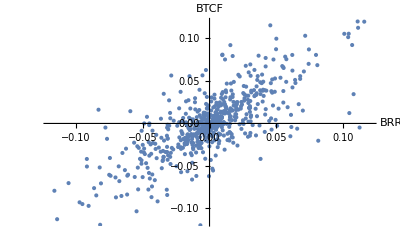

```mathematica
p=ListPlot[{rbrr,rbtc}ᵀ, PlotStyle->Thick,AxesLabel->{"BRR", "BTCF"}]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/scatter.pdf",p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/scatter.pdf

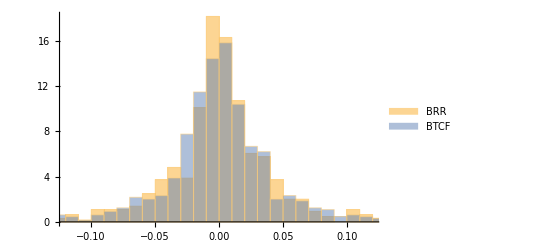

```mathematica
p=Histogram[{rbrr,rbtc}, Automatic, "PDF",ChartLegends->{"BRR", "BTCF"}]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/histograms.pdf",p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/histograms.pdf

```mathematica
{α1,β1,μ1,δ1}=FitNIG[rbrr]
```

{20.1791,-1.11329,0.00228454,0.0350148}

```mathematica
{α2,β2,μ2,δ2}=FitNIG[rbtc]
```

{16.4365,-1.04596,0.00258213,0.0349328}

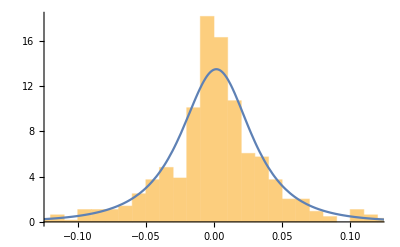
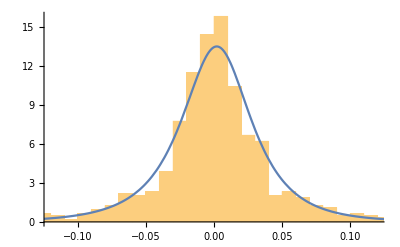

```mathematica
{Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[g[x,α1,β1,μ1,δ1], {x,-0.3,0.3},PlotRange->All]
],
Show[Histogram[rbtc, Automatic, "PDF"],
Plot[g[x,α1,β1,μ2,δ2], {x,-0.3, 0.3}, PlotRange->All]
]
}
```

```mathematica
{α,β,μ1, δ1, μ2, δ2}=FitJointNIG[rbrr,rbtc,Min[α1,α2],Max[α1,α2]]
```

{17.6612,-1.06607,0.00220125,0.030616,0.00262596,0.0375604}

```mathematica
δ=FitCorrelation[rbrr,rbtc,δ1, δ2]
```

0.0267315

Make delta’s incremental (i.e., δ1 refers to delta parameter of Z_1 and likewise for δ2).

```mathematica
δ1=δ1-δ;
δ2=δ2-δ;
```

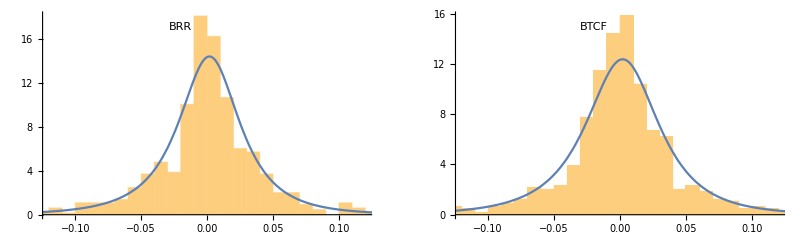

```mathematica
p=GraphicsGrid[{{Show[
Histogram[rbrr, Automatic, "PDF",ChartLabels->{"BRR"}],
Plot[g[x,α,β,μ1,δ+δ1], {x,-0.3,0.3},PlotRange->All]
],
Show[Histogram[rbtc, Automatic, "PDF", ChartLabels->{"BTCF"}],
Plot[g[x,α,β,μ2,δ+δ2], {x,-0.3, 0.3}, PlotRange->All]
]
}}]
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/fittedNIG.pdf",p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/fittedNIG.pdf

#### Hedge

-Graphics-

Direct integration uses the decomposition below to determine the CDF exactly.
-Graphics-
-Graphics-

```mathematica
γ=√(α^2-β^2);
h=0.95;
x=0.01;
Timing[NIntegrate[CDF[NormalDistribution[μ1-h μ2+β w1-h β w2, √((1-h)^2 w+w1+h^2 w2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], w]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], w1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], w2], {w,0,∞},{w1,0,∞}, {w2,0,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{4.09673,0.733644}

The exact PDF to be compared with Fourier Inversion below (which is much faster).

```mathematica
γ=√(α^2-β^2);
h=0.95;
x=0.01;
Timing[NIntegrate[PDF[NormalDistribution[μ1-h μ2+β w1-h β w2, √((1-h)^2 w+w1+h^2 w2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], w]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], w1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], w2], {w,0,∞},{w1,0,∞}, {w2,0,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{4.22536,17.4613}

Exact PDF of hedge via Fourier inversion of characteristic function

```mathematica
Needs["FourierSeries`"]
```

Characteristic function

```mathematica
cf=M[I u,α/(1-h),β/(1-h),0,δ (1-h)] M[I u,α,β,μ1,δ1] M[I u,α/h,-β/h,-h μ2,h δ2];
```

```mathematica
Timing[NInverseFourierTransform[cf, u, x, FourierParameters->{1,1}]]
```

{0.022176,17.3686}

```mathematica
Timing[t=Table[{y,NInverseFourierTransform[cf, u,y, FourierParameters->{1,1}]},{y,-1,x,0.005}];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-186.315}. NIntegrate obtained 1.86901-2.44249×10^-15 ⅈ and 3.91286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-186.315}. NIntegrate obtained 3.22925-1.26565×10^-14 ⅈ and 4.40054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {186.315}. NIntegrate obtained 0.229715+3.9968×10^-15 ⅈ and 4.06258 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{4.97437,Null}

This gives sketchy results for particularly small (and large) arguments.

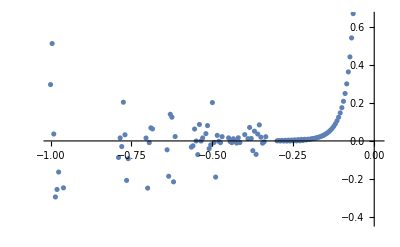

```mathematica
ListPlot[t]
```

Approximate distribution of hedged position by NIG (it’s not exactly NIG because of the scaling with h and if β≠0, but should be close). Match moments.

-Graphics-

```mathematica
g1 = M[u,αh, βh, μh, δh]
```

ⅇ^(δh (√(αh^2-βh^2)-√(αh^2-(βh+u)^2))+μh u)

```mathematica
g2=M[u,α/(1-h),β/(1-h),0,δ (1-h)] M[u,α,β,μ1,δ1] M[-u,α/h,β/h,h μ2,h δ2]
```

exp(0.0102875 (18.5569-√(345.616-(-u-1.12217)^2))+0.00133657 (352.58-√(124767.-(u-21.3213)^2))+0.00388452 (17.629-√(311.918-(u-1.06607)^2))-0.000293415 u)

```mathematica
Timing[sol=NSolve[Flatten[Join[Table[D[g1,{u,r}]==D[g2,{u,r}]/.{u->0}, {r,1,4}],{αh>0,δh>0}]],{αh,βh,μh,δh}]]
```

{19.4093,{{αh→18.1902,μh→-0.000335343,δh→0.0142003,βh→0.446033}}}

```mathematica
{α,β,μ1+(1-h)μ2,δ}
```

{17.6612,-1.06607,0.00233255,0.0267315}

```mathematica
{D[g2, {u,1}]/.{u->0},ENIG[αh,βh,μh,δh]/.sol⟦1⟧}
```

{0.0000129598,0.0000129598}

```mathematica
{D[g2, {u,2}]/.{u->0},VNIG[αh,βh,μh,δh]+ENIG[αh,βh,μh,δh]^2/.sol⟦1⟧,VNIG[αh,βh,-(βh δh)/(√(αh^2-βh^2)),δh]/.sol⟦1⟧}
```

{0.000781361,0.000781361,0.000781361}

```mathematica
Dynamic[x]
```

For extreme values of β, the first approximation (calibrating the parameters) performs better than the second (first-order Taylor approximation of moment-generating function’s exponent).

```mathematica
t1=Timing[Table[{x,NIntegrate[g[y,αh,βh,μh,δh]/.sol[[1]], {y,-∞,x}]}, {x,-0.1, 0.1,0.01}]];
```

Compare to direct integration

```mathematica
γ=√(α^2-β^2);
t2=Timing[Table[{x,NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}]},{x,-0.1, 0.1,0.01}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Second NIG approximation

-Graphics-

```mathematica
t3=Timing[Table[{x,NIntegrate[g[y,α,β,μ1-μ2-(2 δ2 β)/(√(α^2-β^2)), δ1+δ2], {y,-∞,x}]}, {x,-0.1, 0.1,0.01}]];
```

FT stuff; first generate a smooth density function, then integrate

```mathematica
Timing[t4=Table[{y,Max[Re[NInverseFourierTransform[cf, u,y, FourierParameters->{1,1},AccuracyGoal->5]],0]}, {y, -0.5,0.1, 0.01}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-283.95}. NIntegrate obtained 1.27226-1.9873×10^-14 ⅈ and 1.0883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-283.95}. NIntegrate obtained -1.19888-4.16334×10^-15 ⅈ and 1.01482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-283.95}. NIntegrate obtained -0.0146183-9.76996×10^-15 ⅈ and 0.811748 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1.48144,Null}

```mathematica
Timing[it=Interpolation[t4]]
```

{0.000278,InterpolatingFunction[…]}

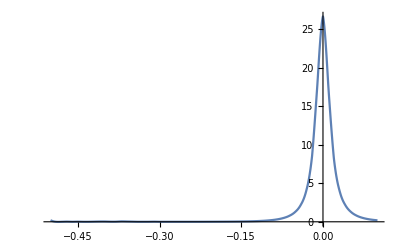

```mathematica
Plot[it[x], {x,-.5,.1},PlotRange->All]
```

```mathematica
it[-0.33]
```

-2.02761×10^-17

```mathematica
Timing[NIntegrate[it[x], {x,-0.5,0.01}]]
```

{0.003588,0.735784}

```mathematica
t5=Timing[Table[{x,NIntegrate[it[y], {y,-0.5,x}]}, {x,-0.1, 0.1,0.01}]];
```

```mathematica
Timing[NIntegrate[1/(2 Pi) Exp[-I u y] cf, {u,-∞, ∞}, {y, -0.5, x}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.735049-8.55583×10^-9 ⅈ and 0.0000231203 for the integral and error estimates.

{9.52299,0.735049-8.55583×10^-9 ⅈ}

This uses Equation (25) from Shiryaev, II.§12 Theorem 3 to calculate the CDF value:

```mathematica
a=0.01; b=-3;
Timing[1/(2Pi) NIntegrate[(Exp[-I u b]-Exp[-I u a])/(I u) cf, {u, -∞,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-48.7522}. NIntegrate obtained 4.7207+0.000501558 ⅈ and 0.457015 for the integral and error estimates.

{0.035173,0.751322+0.0000798254 ⅈ}

```mathematica
Timing[NIntegrate[g[y,αh,βh,μh,δh]/.sol[[1]], {y,-∞,x}]]
```

{0.016285,0.736644}

```mathematica
NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.733644

t1: NIG approximation with αh, βh, μh, δh
t2: direct integration
t3: NIG approximation (Taylor expansion)
t5: Fourier inversion

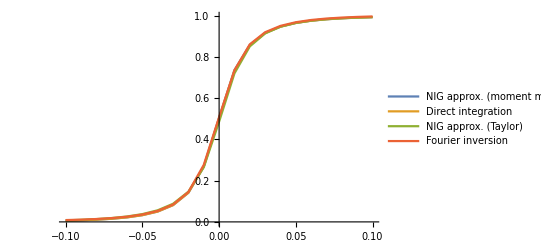

```mathematica
p=ListPlot[{t1⟦2⟧,t2⟦2⟧,t3⟦2⟧,t5⟦2⟧},Joined->True, PlotLegends->Placed[{"NIG approx. (moment matching)", "Direct integration", "NIG approx. (Taylor)", "Fourier inversion"},Below]]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/NIG1.pdf", p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/NIG1.pdf

```mathematica
t2[[2,;;,1]]
```

{-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

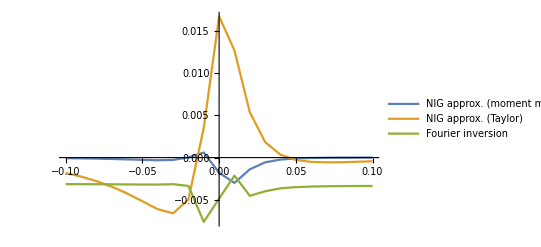

```mathematica
p=ListPlot[{(t2-t1)⟦2,1;;All,2⟧,(t2-t3)⟦2,1;;All,2⟧,(t2-t5)⟦2,1;;All,2⟧},DataRange->t2⟦2,{1,-1},1⟧, Joined->True,PlotRange->All,PlotLegends->Placed[{"NIG approx. (moment matching)", "NIG approx. (Taylor)", "Fourier inversion"},Below]]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/NIG2.pdf", p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/NIG2.pdf

CPU times (plus 18.6 seconds for parameter calibration in NIG approx; plus 1.55 secs for Fourier inversion to generate smooth density)

```mathematica
{t1⟦1⟧,t2⟦1⟧,t3⟦1⟧,t5⟦1⟧}
```

{0.227014,78.5995,0.183336,0.034224}

### PDF stuff (if it’s ever needed)

```mathematica
Timing[t1a=Table[{x,g[x,αh,βh,μh,δh]/.sol[[1]]}, {x,-0.1, 0.1,0.01}];]
```

{0.004982,Null}

```mathematica
γ=√(α^2-β^2);
Timing[t2a=Table[{x,NIntegrate[PDF[NormalDistribution[μ1-h μ2+β w1-h β w2, √((1-h)^2 w+w1+h^2 w2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], w]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], w1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], w2], {w,0,∞},{w1,0,∞}, {w2,0,∞}]},{x,-0.1, 0.1,0.01}];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{77.6485,Null}

```mathematica
cf=M[I u,α/(1-h),β/(1-h),0,δ (1-h)] M[I u,α,β,μ1,δ1] M[I u,α/h,-β/h,-h μ2,h δ2];
```

```mathematica
Timing[t3a=Table[{x,NInverseFourierTransform[g2, u,x, FourierParameters->{1,1}]},{x,-0.1, 0.1,0.01}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained 2.191689711974484`15.954589770191005*^874282338560273+1.871036643371317`15.954589770191005*^874282338560273 ⅈ and 2.191689711974484`15.954589770191005*^874282338560273+1.871036643371317`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained 2.711627180292629`15.954589770191005*^874282338560273+9.75376824366485`15.954589770191005*^874282338560272 ⅈ and 2.711627180292629`15.954589770191005*^874282338560273+9.75376824366485`15.954589770191005*^874282338560272 ⅈ for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained -1.608722423900063`15.954589770191005*^874282338560272-2.877221235157529`15.954589770191005*^874282338560273 ⅈ and -1.608722423900063`15.954589770191005*^874282338560272-2.877221235157529`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.34976,Null}

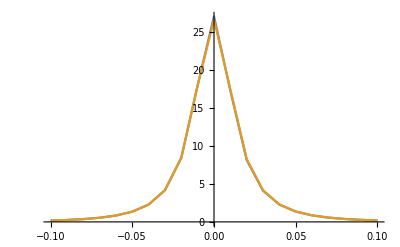

```mathematica
ListPlot[{t1a,t2a,t3a},Joined->True]
```

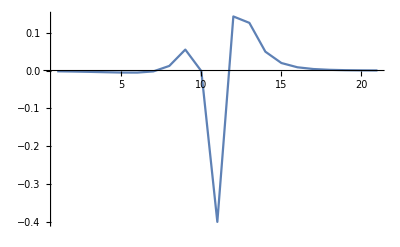

```mathematica
ListPlot[{(t2a-t1a)⟦1;;All,2⟧,(t2a-t3a)⟦1;;All,2⟧},Joined->True,PlotRange->All]
```

```mathematica
NIntegrate[NInverseFourierTransform[g2, u,y, FourierParameters->{1,1},AccuracyGoal->5], {y,-20,x}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.24055}. NIntegrate obtained 1.331596437458312`15.954589770191005*^874282338560273+4.957381758379911`15.954589770191005*^874282338560272 ⅈ and 1.331596437458312`15.954589770191005*^874282338560273+4.957381758379911`15.954589770191005*^874282338560272 ⅈ for the integral and error estimates.

1.331596437458311632277690097`15.954589770191005*^874282338560273+4.95738175837990935033065487`15.653559774527023*^874282338560272 ⅈ

```mathematica
NInverseFourierTransform[g2, u,-0.5, FourierParameters->{1,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained 3.709108684962785`15.954589770191005*^874282338560272-2.857745097457844`15.954589770191005*^874282338560273 ⅈ and 3.709108684962785`15.954589770191005*^874282338560272-2.857745097457844`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

5.9032298167690666710866857`15.954589770191005*^874282338560271-4.54824258357045887892137425`15.954589770191005*^874282338560272 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained -1.818781682893604`15.954589770191005*^874282338560272+2.875969792315752`15.954589770191005*^874282338560273 ⅈ and -1.818781682893604`15.954589770191005*^874282338560272+2.875969792315752`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained 8.466148145314755`15.954589770191005*^874282338560272+2.754546291175525`15.954589770191005*^874282338560273 ⅈ and 8.466148145314755`15.954589770191005*^874282338560272+2.754546291175525`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained 1.76576306200881`15.954589770191005*^874282338560273+2.277358716420905`15.954589770191005*^874282338560273 ⅈ and 1.76576306200881`15.954589770191005*^874282338560273+2.277358716420905`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> (-1. | 1.
0 | 4.58613940912517859137462668`15.954589770191005*^874282338560272) is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

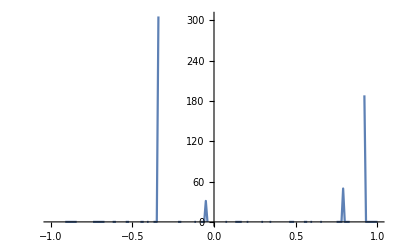

```mathematica
ListPlot[t=Table[{y,Max[Re[NInverseFourierTransform[g2, u,y, FourierParameters->{1,1},AccuracyGoal->5]],0]}, {y, -1,1, 0.01}],Joined->True,PlotRange->All]
```

```mathematica
it=Interpolation[t]
```

InterpolatingFunction[…]

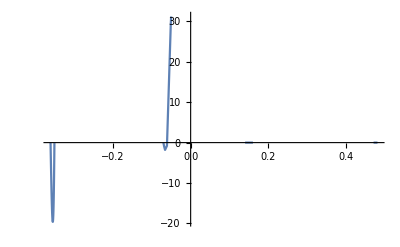

```mathematica
Plot[it[x], {x,-.5,.5},PlotRange->All]
```

```mathematica
it[-0.33]
```

5.8824098411395686760253018`15.954589770191005*^874282338560271

```mathematica
NInverseFourierTransform[g2, u,-0.33, FourierParameters->{1,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained -1.411752600455844`15.954589770191005*^874282338560272-2.878254933178099`15.954589770191005*^874282338560273 ⅈ and -1.411752600455844`15.954589770191005*^874282338560272-2.878254933178099`15.954589770191005*^874282338560273 ⅈ for the integral and error estimates.

-2.2468740478538505581218256`15.954589770191005*^874282338560271-4.58088500093927278640088747`15.954589770191005*^874282338560272 ⅈ

```mathematica
Timing[NIntegrate[it[x], {x,-0.5,0.01}]]
```

{0.004349,6.1513669873120182930440587`15.954589770191005*^874282338560271}

```mathematica
Timing[NIntegrate[1/(2 Pi) Exp[-I u y] g2, {u,-∞, ∞}, {y, -0.5, x}]]
```

NIntegrate::inumri: The integrand ⅇ^(«1»)/(2 π) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (0. | -4.0247×10^31
-0.5 | 0.01).

{0.025591,NIntegrate[(g2 exp(-ⅈ u y))/(2 π),{u,-∞,∞},{y,-0.5,x}]}

This uses Equation (25) from Shiryaev, II.§12 Theorem 3 to calculate the CDF value:

```mathematica
a=0.01; b=-3;
Timing[1/(2Pi) NIntegrate[(Exp[-I u b]-Exp[-I u a])/(I u) g2, {u, -∞,∞}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-8.04426×10^11}. NIntegrate obtained -2.62060434349721`15.954589770191005*^874282338560254-7.773050413966376`15.954589770191005*^874282338560254 ⅈ and -2.62060434349721`15.954589770191005*^874282338560254-7.773050413966376`15.954589770191005*^874282338560254 ⅈ for the integral and error estimates.

{0.033659,-4.170821351556721075050307482`15.954589770191005*^874282338560253-1.2371193962852517330789914953`15.954589770191005*^874282338560254 ⅈ}

```mathematica
Timing[NIntegrate[g[y,αh,βh,μh,δh]/.sol[[1]], {y,-∞,x}]]
```

{0.016018,0.736644}

```mathematica
NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.733644

### NIG approximation of hedge distribution

```mathematica
Clear[α,β]
```

```mathematica
Simplify[e1=√(α^2-(β+u)^2)-√(α^2-(β-u)^2)]
```

√(α^2-(β+u)^2)-√(α^2-(u-β)^2)

Taylor expansions

```mathematica
Series[e1, {u,0,1}]
```

-(2 β u)/(√(α^2-β^2))+O(u^2)

```mathematica
Plot[{e1, Normal[Series[e1, {u,0,1}]]}/.u->x, {x,-3,3}]
```

-Graphics-

```mathematica
Clear[α,β, μ1,δ1,μ2,δ2]
```

```mathematica
t1=M[u,α,β,μ1,δ1] M[-u,α,β,μ2,δ2]
```

exp(δ1 (√(α^2-β^2)-√(α^2-(β+u)^2))+δ2 (√(α^2-β^2)-√(α^2-(β-u)^2))+μ1 u-μ2 u)

```mathematica
t2=M[u,α,β,μ1-μ2-(2 δ2 β)/(√(α^2-β^2)),δ1+δ2]
```

exp((δ1+δ2) (√(α^2-β^2)-√(α^2-(β+u)^2))+u (-(2 β δ2)/(√(α^2-β^2))+μ1-μ2))

```mathematica
Table[Simplify[{D[t1,{u,r}]- D[t2,{u,r}]}/.u->0], {r,1,4}]
```

(0
0
-(6 α^2 β δ2)/((α^2-β^2)^(5/2))
(24 α^2 β δ2 (√(α^2-β^2) (μ2-μ1)+β (δ2-δ1)))/((α^2-β^2)^3))